# Pentacene Triplet SubLevels under Magnetic field

## Calculation

```mathematica
Angular momentum in Martix Form.nb
```

```mathematica
ℏ=1;
Sx={{0,1/(√2),0},{1/(√2),0,1/(√2)},{0,1/(√2),0}};
Sy={{0,-ⅈ/(√2),0},{ⅈ/(√2),0,-ⅈ/(√2)},{0,ⅈ/(√2),0}};
Sz={{1,0,0},{0,0,0},{0,0,-1}};
Rot[θ_,ϕ_, α_]:={{(Cos[α/2]-ⅈ Cos[θ] Sin[α/2])^2,(ⅇ^(-ⅈ ϕ) ((-1+Cos[α]) Cos[θ]-ⅈ Sin[α]) Sin[θ])/(√2),-ⅇ^(-2 ⅈ ϕ) Sin[α/2]^2 Sin[θ]^2},{(ⅇ^(ⅈ ϕ) ((-1+Cos[α]) Cos[θ]-ⅈ Sin[α]) Sin[θ])/(√2),Cos[θ]^2+Cos[α] Sin[θ]^2,-(ⅇ^(-ⅈ ϕ) ((-1+Cos[α]) Cos[θ]+ⅈ Sin[α]) Sin[θ])/(√2)},{-ⅇ^(2 ⅈ ϕ) Sin[α/2]^2 Sin[θ]^2,√2 ⅇ^(ⅈ ϕ) Sin[α/2] (-ⅈ Cos[α/2]+Cos[θ] Sin[α/2]) Sin[θ],1/2 (Cos[α] (1+Cos[θ]^2)+2 ⅈ Cos[θ] Sin[α]+Sin[θ]^2)}}(* Right Hand *)
```

```mathematica
(* the Zero Field Split Hamiltonain in crystal corrdinate is *)
Clear[α,β,γe]
HzfsCys=α(Sz.Sz-2/3 IdentityMatrix[3])+β(Sx.Sx-Sy.Sy);
(* The Zeeman Mailtonain *) 
Hb[B_]:=γe B Sz
```

```mathematica
(* B // Z *)
ωZ=Eigensystem[HzfsCys+Hb[B]][[1]]
VZ=Eigensystem[HzfsCys+Hb[B]][[2]]
```

{-(2 α)/3,1/3 (α-3 √(β^2+B^2 γe^2)),1/3 (α+3 √(β^2+B^2 γe^2))}

{{0,1,0},{-(-B γe+√(β^2+B^2 γe^2))/β,0,1},{-(-B γe-√(β^2+B^2 γe^2))/β,0,1}}

```mathematica
(* B//Y *)
ωY=Eigensystem[Rot[π/2,0,π/2].HzfsCys.Inverse[Rot[π/2,0,π/2]]+Hb[B]][[1]]
VY=Eigensystem[Rot[π/2,0,π/2].HzfsCys.Inverse[Rot[π/2,0,π/2]]+Hb[B]][[2]]
```

{1/3 (α+3 β),1/6 (-α-3 β-3 √(α^2-2 α β+β^2+4 B^2 γe^2)),1/6 (-α-3 β+3 √(α^2-2 α β+β^2+4 B^2 γe^2))}

{{0,1,0},{-(2 B γe-√(α^2-2 α β+β^2+4 B^2 γe^2))/(α-β),0,1},{-(2 B γe+√(α^2-2 α β+β^2+4 B^2 γe^2))/(α-β),0,1}}

```mathematica
Rot[π/2,π/2,π/2]2//MatrixForm
```

(1 | -√2 | 1
√2 | 0 | -√2
1 | √2 | 1)

```mathematica
(* B//X *)
ωX=Eigensystem[Rot[π/2,π/2,π/2].HzfsCys.Inverse[Rot[π/2,π/2,π/2]]+Hb[B]][[1]]
VX=Eigensystem[Rot[π/2,π/2,π/2].HzfsCys.Inverse[Rot[π/2,π/2,π/2]]+Hb[B]][[2]]
```

{1/3 (α-3 β),1/6 (-α+3 β-3 √(α^2+2 α β+β^2+4 B^2 γe^2)),1/6 (-α+3 β+3 √(α^2+2 α β+β^2+4 B^2 γe^2))}

{{0,1,0},{-(-2 B γe+√(α^2+2 α β+β^2+4 B^2 γe^2))/(α+β),0,1},{-(-2 B γe-√(α^2+2 α β+β^2+4 B^2 γe^2))/(α+β),0,1}}

```mathematica
(* B at θ, ϕ *)
H[θ_,ϕ_,γ_,B_]:=Rot[0,0,ϕ].Rot[π/2,π/2,θ].Rot[0,0,γ].HzfsCys.Inverse[Rot[0,0,ϕ].Rot[π/2,π/2,θ].Rot[0,0,γ]]+Hb[B]//FullSimplify
Eigensystem[H[θ,ϕ,γ,B]][[1]]
```

{Root[8 α^3-72 α β^2-18 B^2 α γe^2-54 B^2 β γe^2 Cos[2 γ]+27 B^2 β γe^2 Cos[2 γ-2 θ]-54 B^2 α γe^2 Cos[2 θ]+27 B^2 β γe^2 Cos[2 γ+2 θ]+(-36 α^2-108 β^2-108 B^2 γe^2) #1+108 #1^3&,1],Root[8 α^3-72 α β^2-18 B^2 α γe^2-54 B^2 β γe^2 Cos[2 γ]+27 B^2 β γe^2 Cos[2 γ-2 θ]-54 B^2 α γe^2 Cos[2 θ]+27 B^2 β γe^2 Cos[2 γ+2 θ]+(-36 α^2-108 β^2-108 B^2 γe^2) #1+108 #1^3&,2],Root[8 α^3-72 α β^2-18 B^2 α γe^2-54 B^2 β γe^2 Cos[2 γ]+27 B^2 β γe^2 Cos[2 γ-2 θ]-54 B^2 α γe^2 Cos[2 θ]+27 B^2 β γe^2 Cos[2 γ+2 θ]+(-36 α^2-108 β^2-108 B^2 γe^2) #1+108 #1^3&,3]}

## Lattice Drawing

```mathematica
(* Naphthalene *)
Lattics[spac_, n1_,n2_]:=Flatten[Table[Total[spac]/2+k1 spac[[1]]+k2 spac[[2]] +k3 spac[[3]],{k1,n1,n2},{k2,n1,n2},{k3,n1,n2}],2];
pentacene=Table[2.8 Sin[π/3]{j,0,0}+1.4{Sin[(i π)/3],Cos[(i π)/3],0},{j,-2,2,1},{i,1,7}];
naphthalene=Table[2.8 Sin[π/3]{j,0,0}+1.4{Sin[(i π)/3],Cos[(i π)/3],0},{j,-1/2,1/2,1},{i,1,7}];
napSpace={{0,0,8.235},{ 0,6.003,0},{ 8.658Sin[122 °],0,8.658Cos[122 °]}};
(* Para- Terphenyl *)
paraTerphenyl=Join[Table[1.4 3 {j,0,0}+If[j==0,1.4{Cos[i π/3],0,Sin[i π/3]},1.4{Cos[i π/3],Sin[i π/3],0}],{j,-1,1},{i,0,6}],{{{1.4,0,0},{1.4 2,0,0}},{-{1.4,0,0},-{1.4 2,0,0}}}];
pTSpace={{0,0,8.1},{0,5.6,0},{13.6Sin[92.1 °],0,13.6Cos[92.1 °]}};
```

```mathematica
Draw[crystal_,dopAng_,space_,n1_,n2_]:=
Module[{poiLat,dopLat},
Manipulate[Graphics3D[{
poiLat=Lattics[space,n1,n2];
dopLat=Map[Total[space]/2+#&,Lattics[space,n1,n2-1],{1}];
Arrow[{{0,0,0},{10,0,0}}],Text["x",{10.1,0,0}],
Arrow[{{0,0,0},{0,5,0}}],Text["y",{0,5.1,0}],
Arrow[{{0,0,0},{0,0,10}}],Text["z",{0,0,10.1}],
Rotate[Rotate[Rotate[{
{Blue,Table[Rotate[Line[Map[poiLat[[i]]+# &,crystal,{2}]],ArcCos[Normalize[space[[3]]][[3]]]-π/2, {0,1,0},poiLat[[i]]],{i,1,Length[poiLat]}]},
{Red,
Arrow[{-Total[space]/2,-Total[space]/2+space[[1]]}],Text["a",-Total[space]/2+space[[1]]],
Arrow[{-Total[space]/2,-Total[space]/2+space[[2]]}],Text["b",-Total[space]/2+space[[2]]],
Arrow[{-Total[space]/2,-Total[space]/2+space[[3]]}],Text["c",-Total[space]/2+space[[3]]]
},
{Green,Dashed,
Line[Map[Total[space]/2+#&,{{0,0,0},-space[[1]], -space[[1]]-space[[2]],-space[[2]],{0,0,0},-space[[3]],-space[[3]]-space[[1]],-space[[1]]},{1}]],
Line[Map[Total[space]/2+#&,{-space[[2]],-space[[2]]-space[[3]],-space[[3]]},{1}]]},
Purple,
Rotate[{Arrow[{{0,0,0},{7,0,0}}],Text["X",{7.1,0,0}],
Arrow[{{0,0,0},{0,3,0}}],Text["Y",{0,3.1,0}],
Arrow[{{0,0,0},{0,0,3}}],Text["Z",{0,0,3.1}]},dopAng,{0,1,0}],
Opacity[0.5],
Table[Rotate[Polygon[Map[dopLat[[i]]+#&,pentacene,{2}]]
,dopAng, {0,1,0},dopLat[[i]]],{i,1, Length[dopLat]}]
},γ,{0,0,1}],θ-dopAng,{0,1,0}],ϕ,{0,0,1}]
},ImageSize->400],{θ,0, π/2},{ϕ,0, π/2},{γ,0, π/2}]]
Draw2[crystal_,dopAng_,space_,cell_]:=
Module[{poiLat},
Manipulate[Graphics3D[{
poiLat=Lattics[space,-1-cell+1,0+cell-1];
Arrow[{{0,0,0},{10,0,0}}],Text["x",{10.1,0,0}],
Arrow[{{0,0,0},{0,5,0}}],Text["y",{0,5.1,0}],
Arrow[{{0,0,0},{0,0,10}}],Text["z",{0,0,10.1}],
Rotate[Rotate[Rotate[{
{Blue,Table[Rotate[Line[Map[poiLat[[i]]+# &,crystal,{2}]],ArcCos[Normalize[space[[3]]][[3]]]-π/2, {0,1,0},poiLat[[i]]],{i,1,Length[poiLat]}]},
{Red,
Arrow[{-Total[space]/2,-Total[space]/2+space[[1]]}],Text["a",-Total[space]/2+space[[1]]],
Arrow[{-Total[space]/2,-Total[space]/2+space[[2]]}],Text["b",-Total[space]/2+space[[2]]],
Arrow[{-Total[space]/2,-Total[space]/2+space[[3]]}],Text["c",-Total[space]/2+space[[3]]]
},
{Green,Dashed,
Line[Map[Total[space]/2+#&,{{0,0,0},-space[[1]], -space[[1]]-space[[2]],-space[[2]],{0,0,0},-space[[3]],-space[[3]]-space[[1]],-space[[1]]},{1}]],
Line[Map[Total[space]/2+#&,{-space[[2]],-space[[2]]-space[[3]],-space[[3]]},{1}]]},
Purple,
Rotate[{Arrow[{{0,0,0},{7,0,0}}],Text["X",{7.1,0,0}],
Arrow[{{0,0,0},{0,3,0}}],Text["Y",{0,3.1,0}],
Arrow[{{0,0,0},{0,0,3}}],Text["Z",{0,0,3.1}]},dopAng,{0,1,0}],
Opacity[0.5],
Rotate[Polygon[pentacene],dopAng, {0,1,0}]
},γ,{0,0,1}],θ-dopAng,{0,1,0}],ϕ,{0,0,1}]
},ImageSize->400],{θ,0, π/2},{ϕ,0, π/2},{γ,0, π/2}]]
```

```mathematica
Draw2[paraTerphenyl,0, pTSpace,1]
```

```mathematica
Draw2[naphthalene,023°, napSpace,3]
```

## Plot

```mathematica
Module[{α,β,γe},
α=1381.5 (* MHz *);
β=-42.5 (* MHz *);
γe=28024.95; (* MHz/T = μe/ℏ*)
g[θ_,ϕ_,γ_,B_]:={Root[8 α^3-72 α β^2-18 B^2 α γe^2-54 B^2 β γe^2 Cos[2 γ]+27 B^2 β γe^2 Cos[2 γ-2 θ]-54 B^2 α γe^2 Cos[2 θ]+27 B^2 β γe^2 Cos[2 γ+2 θ]+(-36 α^2-108 β^2-108 B^2 γe^2) #1+108 #1^3&,1],Root[8 α^3-72 α β^2-18 B^2 α γe^2-54 B^2 β γe^2 Cos[2 γ]+27 B^2 β γe^2 Cos[2 γ-2 θ]-54 B^2 α γe^2 Cos[2 θ]+27 B^2 β γe^2 Cos[2 γ+2 θ]+(-36 α^2-108 β^2-108 B^2 γe^2) #1+108 #1^3&,2],Root[8 α^3-72 α β^2-18 B^2 α γe^2-54 B^2 β γe^2 Cos[2 γ]+27 B^2 β γe^2 Cos[2 γ-2 θ]-54 B^2 α γe^2 Cos[2 θ]+27 B^2 β γe^2 Cos[2 γ+2 θ]+(-36 α^2-108 β^2-108 B^2 γe^2) #1+108 #1^3&,3]}
]
```

```mathematica
42.577*0.0644
```

2.74196

```mathematica
0.06444/2750
```

0.0000234327

```mathematica
(g[π/2,0,0,0.0644]-g[π/2,0,0,0.0644+0.003]).{-1,1,0}
```

-79.0394

### B // X Y Z

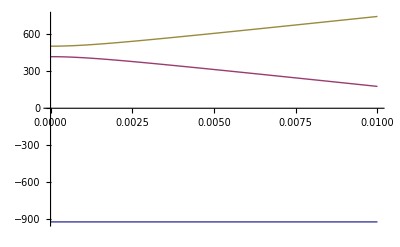

```mathematica
Plot[ωZ,{B,0,0.01}]
```

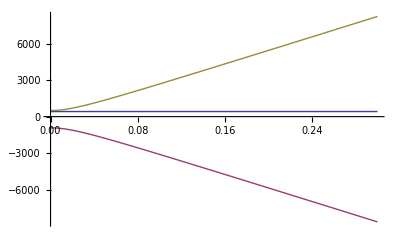

```mathematica
Plot[ωY,{B,0,0.3}]
```

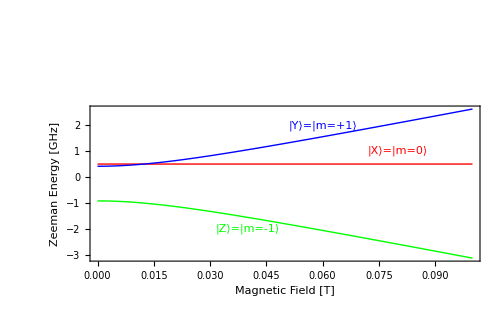

```mathematica
Module[{α,β,γe},
α=1381.5 (* MHz *);
β=-42.5 (* MHz *);
γe=28024.95; (* MHz/T = μe/ℏ*)Plot[Evaluate[{1/3 (α-3 β),1/6 (-α+3 β-3 √(α^2+2 α β+β^2+4 B^2 γe^2)),1/6 (-α+3 β+3 √(α^2+2 α β+β^2+4 B^2 γe^2))}/1000],{B,0,0.1}, PlotStyle->{Red,Green, Blue}, Frame->True, FrameLabel->{Style["Magnetic Field [T]",Large],Style["Zeeman Energy [GHz]",Large]}, ImageSize->500,
 Epilog->{
{Red,Text[Style["|X⟩=|m=0⟩", Medium],{0.08,1}]},
{Blue,Text[Style["|Y⟩=|m=+1⟩", Medium],{0.06,2}]},
{Green,Text[Style["|Z⟩=|m=-1⟩", Medium],{0.04,-2}]},
Text[Style["B // X", Large],{0.05,5}]
}]]
```

### General

```mathematica
Manipulate[TableForm[
{Plot[Evaluate[g[θ,ϕ,γ,B]/1000],{B,0,0.1},PlotStyle->{Red,Green, Blue}, Frame->True, FrameLabel->{Style["Magnetic Field [T]",Large],Style["Zeeman Energy [GHz]",Large]}, ImageSize->500,
 Epilog->{
Text[Style["|X⟩=|m=0⟩", Medium],{0.07,1}],
Text[Style["|Y⟩=|m=+1⟩", Medium],{0.06,2}],
Text[Style["|Z⟩=|m=-1⟩", Medium],{0.06,-2}]}],
Graphics3D[{
Arrow[{{0,0,0},{10,0,0}}],Text["x",{10.1,0,0}],
Arrow[{{0,0,0},{0,5,0}}],Text["y",{0,5.1,0}],
Arrow[{{0,0,0},{0,0,10}}],Text["z",{0,0,10.1}],
Rotate[Rotate[Rotate[{
Purple,
Arrow[{{0,0,0},{7,0,0}}],Text["X",{7.1,0,0}],
Arrow[{{0,0,0},{0,3,0}}],Text["Y",{0,3.1,0}],
Arrow[{{0,0,0},{0,0,3}}],Text["Z",{0,0,3.1}],
Opacity[0.5],Polygon[pentacene]
},γ,{0,0,1}],θ,{0,1,0}],ϕ,{0,0,1}]
},ImageSize->400]
},TableDirections->Row],{θ,0, π/2},{ϕ,0, π/2},{γ,0, π/2}]
```

## Numerical

```mathematica
Manipulate[Module[{α,β,γe},
α=1381.5 (* MHz *);
β=-42.5 (* MHz *);
γe=28024.95; (* MHz/T = μe/ℏ*)
TableForm[{TableForm[{
{{"θ,ϕ ="},{θ 180/π,ϕ 180/π},"B="<>ToString[B]<>"[T]" },
{"ω_-"," ω_0","ω_+"},
g[θ,ϕ,γ,B],
Sort[{1/3 (α-3 β),1/6 (-α+3 β-3 √(α^2+2 α β+β^2+4 B^2 γe^2)),1/6 (-α+3 β+3 √(α^2+2 α β+β^2+4 B^2 γe^2))},Less],
Sort[{1/3 (α+3 β),1/6 (-α-3 β-3 √(α^2-2 α β+β^2+4 B^2 γe^2)),1/6 (-α-3 β+3 √(α^2-2 α β+β^2+4 B^2 γe^2))},Less],
Sort[{-(2 α)/3,1/3 (α-3 √(β^2+B^2 γe^2)),1/3 (α+3 √(β^2+B^2 γe^2))},Less],
{"ω_--ω_0"," ω_0-ω_+","ω_+-ω_-"},
{{-1,1,0}.g[θ,ϕ,γ,B],{0,1,-1}.g[θ,ϕ,γ,B],{1,0,-1}.g[θ,ϕ,γ,B]}
},TableAlignments->Center,TableDepth->2],
Graphics3D[{
Arrow[{{0,0,0},{10,0,0}}],Text["x",{10.1,0,0}],
Arrow[{{0,0,0},{0,5,0}}],Text["y",{0,5.1,0}],
Arrow[{{0,0,0},{0,0,10}}],Text["z",{0,0,10.1}],
Red,Arrow[{{0,0,0},10{Cos[ϕ]Sin[θ], Sin[ϕ]Sin[θ], Cos[θ]}}],
Rotate[Rotate[Rotate[
{Purple,Opacity[0.5],Polygon[pentacene]}
,γ,{0,0,1}],θ,{0,1,0}],ϕ,{0,0,1}]
},ImageSize->400]
},TableDirections->Row]
],{{B,0.06},0,0.3},{{θ,0},0, π/2},{ϕ,0, π/2},{γ,0, π/2}]
```

```mathematica
γp=42.5764; (* MHz/T *)
ESRlower[θ_,ϕ_,γ_,B_]:={-1,1,0}.g[θ,ϕ,γ,B]
Mag[θ_,ϕ_,γ_,esr_]:=Drop[Sort[h/.Chop[Solve[ESRlower[θ,ϕ,γ,h]==esr,h]//N],Greater],-3]
NMR[B_]:=γp B
CalAll[θ_,ϕ_,γ_,esr_]:=TableForm[
{{"Mircowave frequency [GHz]: ",esr/1000//N},
{"      magnetic filed [mT]: ",temp= Mag[θ,ϕ,γ,esr]},
{"      NMR freqeuncy [MHz]: ",Table[ NMR[temp[[i]]],{i,1,3}]},
{" Lower MW freqeuncy [GHz]: ",Table[ ESRlower[θ,ϕ,γ,temp[[i]]],{i,1,3}]},
{" Higer MW freqeuncy [GHz]: ",Table[ g[θ,ϕ,γ,temp[[i]]][[3]]-g[θ,ϕ,γ,temp[[i]]][[2]],{i,1,3}]},
{"Bigger MW freqeuncy [GHz]: ",Table[ g[θ,ϕ,γ,temp[[i]]][[3]]-g[θ,ϕ,γ,temp[[i]]][[1]],{i,1,3}]}},TableDepth->2]
Cal[θ_,ϕ_,γ_,esr_]:=TableForm[
{{"Mircowave frequency [GHz]: ",esr/1000//N},
{"      magnetic filed [mT]: ",(temp= Mag[θ,ϕ,γ,esr])[[2]]},
{"      NMR freqeuncy [MHz]: ",NMR[temp[[2]]]}}]
CalH[θ_,ϕ_,γ_,B_]:=TableForm[{
{"      magnetic filed [mT]: ",B},
{"Mircowave frequency [GHz]: ",ESRlower[θ,ϕ,γ,B]/1000},
{"      NMR freqeuncy [MHz]: ",NMR[B]}}]
CalNMR[θ_,ϕ_,γ_,nmr_]:=TableForm[{
{"      NMR freqeuncy [MHz]: ",nmr},
{"      magnetic filed [mT]: ",nmr/γp},
{"Mircowave frequency [GHz]: ",ESRlower[θ,ϕ,γ,nmr/γp]/1000}}]
P[n1_,n2_]:=(n1-n2)/(n1+n2)//N
```

```mathematica
CalAll[π/2,0,0,2700]
```

Mircowave frequency [GHz]:  | 2.7
      magnetic filed [mT]:  | {0.120928,0.0651803,0.0418303}
      NMR freqeuncy [MHz]:  | {5.14868,2.77514,1.78098}
 Lower MW freqeuncy [GHz]:  | {4209.,2700.,2104.5}
 Higer MW freqeuncy [GHz]:  | {2700.,1191.,595.5}
Bigger MW freqeuncy [GHz]:  | {6909.,3891.,2700.}

```mathematica
Cal[π/2,0,0,2700]
```

Mircowave frequency [GHz]:  | 2.7
      magnetic filed [mT]:  | 0.0651803
      NMR freqeuncy [MHz]:  | 2.77514

```mathematica
CalH[90 π/180,0,0,0.0645]
```

magnetic filed [mT]:  | 0.0645
Mircowave frequency [GHz]:  | 2.68211
      NMR freqeuncy [MHz]:  | 2.74618

```mathematica
CalNMR[90 π/180,0,π/2,12.8]
```

NMR freqeuncy [MHz]:  | 12.8
      magnetic filed [mT]:  | 0.300636
Mircowave frequency [GHz]:  | 9.08234

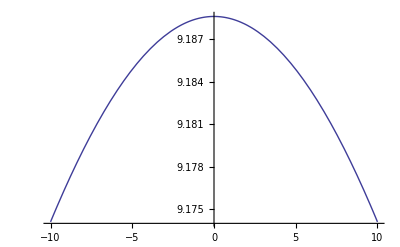

```mathematica
Plot[ESRlower[π/2,π/2,γ π/90,0.3]/1000,{γ,-10,10}]
```

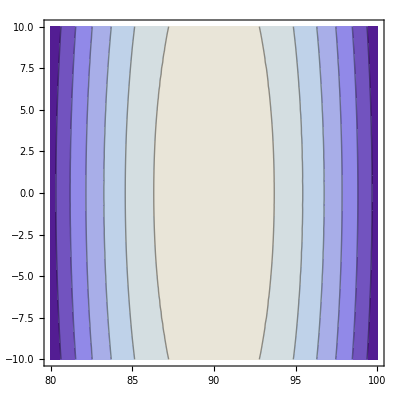

```mathematica
ContourPlot[ESRlower[θ π/180,π/2,γ π/180,0.3]/1000,{θ,80,100},{γ,-10,10}]
```